```mathematica
k=3;
```

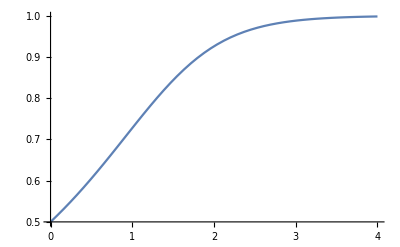

```mathematica
baseSol =NDSolve[{w'[t] ==w[t]^(k-1) - w[t]^(k+1), w[0]==0.5}, w[t], {t, 0, 100}];
Plot[w[t]/.baseSol,{t,0,4}]
```

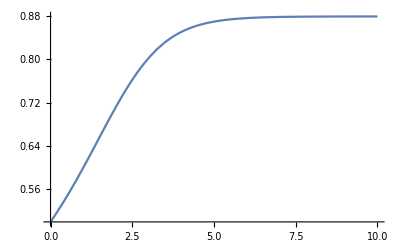

```mathematica
λ = 0.2;
constSol =NDSolve[{w'[t] ==w[t]^(k-1) - w[t]^(k+1) - λ*w[t], w[0]==0.5}, w[t], {t, 0, 10}];
Plot[w[t]/.constSol,{t,0,10}]
```

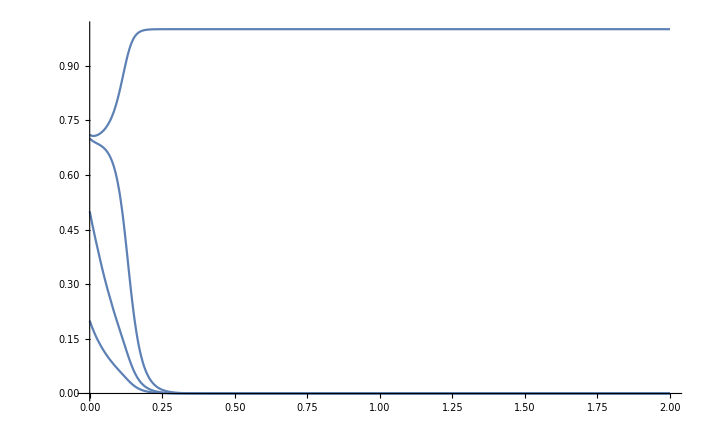

{2.53984,2.22236,2.53984,0.952441}

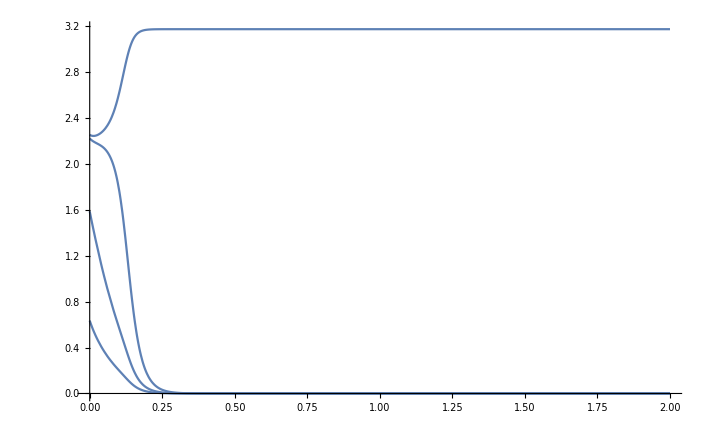

```mathematica
k=5;
{a1,a2,a3, a4}={2, 2, 2, 2};
simulSol =NDSolve[{
w1'[t] ==a1^k*(w1[t]^(k-1) - w1[t]^(k+1) - w1[t]*((a2/a1*w2[t])^k + (a3/a1*w3[t])^k + (a4/a1*w4[t])^k)),
w2'[t] ==a2^k*(w2[t]^(k-1) - w2[t]^(k+1) - w2[t]*((a1/a2*w1[t])^k + (a3/a2*w3[t])^k + (a4/a2*w4[t])^k)),
w3'[t] ==a3^k*(w3[t]^(k-1) - w3[t]^(k+1) - w3[t]*((a2/a3*w2[t])^k + (a1/a3*w1[t])^k + (a4/a3*w4[t])^k)),
w4'[t] ==a4^k*(w4[t]^(k-1) - w4[t]^(k+1) - w4[t]*((a3/a4*w3[t])^k + (a1/a4*w1[t])^k + (a2/a4*w2[t])^k)),
w1[0]==0.71, w2[0]==0.5, w3[0]==0.2, w4[0]==0.7}, {w1[t], w2[t],w3[t],w4[t]}, {t, 0, 100}];
Plot[{w1[t], w2[t], w3[t], w4[t]}/.simulSol,{t,0,2}]
{a1, a2, a3, a4}^(k/(k-2)){0.8, 0.7, 0.8, 0.3}//N
Plot[{a1, a2, a3, a4}^(k/(k-2))*{w1[t], w2[t], w3[t], w4[t]}/.simulSol,{t,0,2}]
```

```mathematica
w1[t]^2 + w2[t]^2 + w3[t]^2+w4[t]^2/.simulSol/.t->0
```

{1.0101}

```mathematica
Assuming[Element[n, Integers]&&n>= 3&&0≤ a≤ 1,
DSolve[{w'[t] ==w[t]^(n-1) - w[t]^(n+1), w[0]==a}, w[t], t]]
```

{{w[t]→InverseFunction[(Hypergeometric2F1[1,1-n/2,2-n/2,#1^2] #1^(2-n))/(-2+n)&][-t+(a^(2-n) Hypergeometric2F1[1,1-n/2,2-n/2,a^2])/(-2+n)]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{w[t]→(-0.333333+ⅇ^(2 t))/(0.333333+ⅇ^(2 t))}}

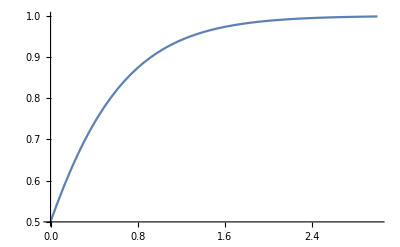

```mathematica
DSolve[{w'[t] ==1-w[t]^2, w[0]==0.5}, w[t], t]
Plot[w[t]/.%,{t,0,3}]
```

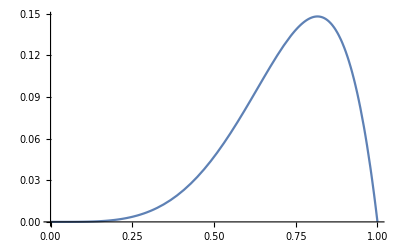

```mathematica
Plot[x^4(1-x^2), {x, 0, 1}]
```

```mathematica
Assuming[0<a<1,DSolve[{w'[t] ==1-w[t]^2, w[0]==a}, w[t], t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{w[t]→(-1+a+ⅇ^(2 t)+a ⅇ^(2 t))/(1-a+ⅇ^(2 t)+a ⅇ^(2 t))}}

```mathematica
eqGen[a_, w_,k_, j_]:=(
w[[j]]'[t]==
Total@MapThread[(#1^(k-1)*Norm[#2]^(k-1)*Dot[#2, a[[j]]])&,{Through@w[t], a}]/Norm[a[[j]]]-
w[[j]][t]*Total@MapThread[#1^k*Norm[#2]^k&, {Through@w[t], a}]
)
```

```mathematica
eqGenUnPet[a_, w_,k_, j_]:=(
w[[j]]'[t]==
w[[j]][t]^(k-1)*Norm[a[[j]]]^k-
w[[j]][t]*Total@MapThread[#1^k*Norm[#2]^k&, {Through@w[t], a}]
)
```

```mathematica
n=100;
d=20;
k=4;
indices=Range[n];
a =RandomVariate[NormalDistribution[], {n, d}];
w = Symbol["w" <> ToString[#]]&/@indices;
x0={1}~Join~Table[0, d-1];
w0=Dot[x0,#]/Norm[#]&/@a;
```

```mathematica
eqsUnPet = (eqGenUnPet[a, w, k, #]&/@indices) ~Join ~Thread[Through@w[0]==w0];
solnUnPet=NDSolve[eqsUnPet,Through@w[t], {t, 0, 100}];

eqsPet = (eqGen[a, w, k, #]&/@indices) ~Join ~Thread[Through@w[0]==w0];
solnPet=NDSolve[eqsPet,Through@w[t], {t, 0, 100}];

maxInd = Ordering[Abs/@First[Through@w[t]/.solnUnPet]/.t->5,-1]//First;
```

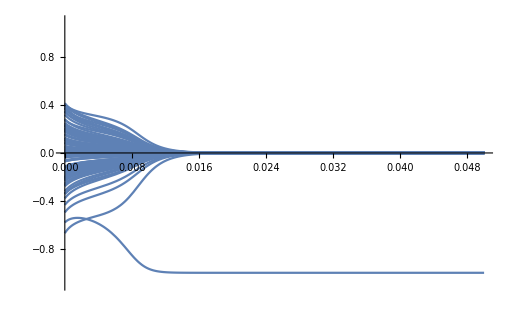

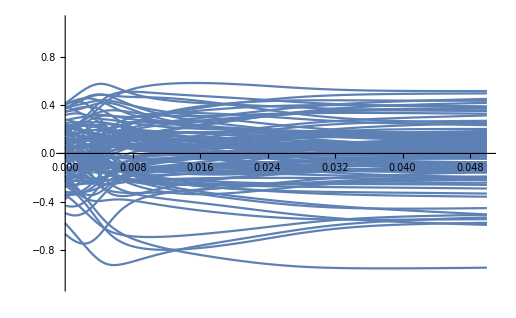

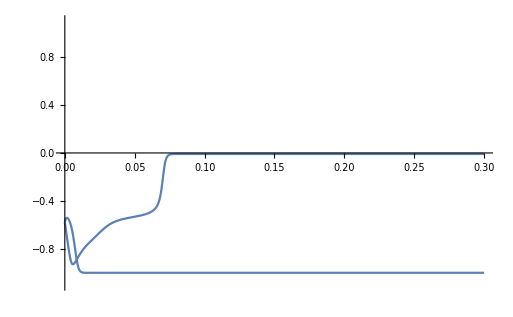

```mathematica
tmax=0.05;

Plot[Through@w[t]/.solnUnPet,{t,0,tmax}, PlotRange->{-1.1, 1.1}]
Plot[Through@w[t]/.solnPet,{t,0,tmax}, PlotRange->{-1.1, 1.1}]
Plot[(Symbol["w" <> ToString[maxInd]][t]/.solnUnPet) ~Join~(Symbol["w" <> ToString[maxInd]][t]/.solnPet) , {t, 0,0.3}, PlotRange->{-1.1, 1.1}]
```

```mathematica
a[[3]].a[[10]]/(Norm[a[[3]]]*Norm[a[[10]]])
```

-0.346836

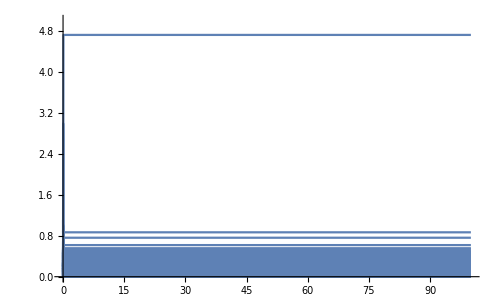

```mathematica
Plot[-Log[1-Abs[Through@w[t]]/.solnPet],{t,0,100}, PlotRange->{0, 5}]
```

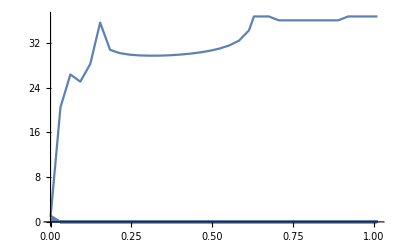

```mathematica
Plot[-Log[1-Abs[Through@w[t]]/.solnUnPet],{t,0,100}, PlotRange->All]
```